## polygonConfigSpace.nb Configuration Space for positioning two particles in a bounded polygon By Jingang Shi <13437170648@163.com>, Aaron Becker and Shiva Shahrokhi

### Plan: Draw polygons. Make list of vertices. For each vertex, move to (0,0), and record positions of all other vertices Take the convex hull of each Derive a formula for ConvexHull (even sided with radius r gives same polygon with radius 2r. An n-sided, n odd with radius r and apothem a gives a 2n-sided with apothem a+r) If locator outside this shape, force it to be at the edge of the polygon. Then place either vertex or side of shape to overlap the locator. , ‘ 1.) plot of the ratio for area of ΔConfigSpace/ConfigSpace. n= 3, ratio is 6. if n is even, ratio is 4, Limit is 4. DONE :) 1.) code to add the two-move reachable set of configurations 2.) draw the configurations on the left and the Delta-space on the right 3.) add a locator for the two particles in the workspace’s start and end 4.) draw the current and goal Delta-configurations on the right 5.) draw one reachable set (there will be n for an n-sided polygon) 6.) draw all the reachable sets 7.)etc. Journal Paper: 1.) reachable sets for regular polygons in 2D 2.) Extend algorithm for regular polygons 3.) Demonstrate this for circles 4.) Extend to 3D (a rectangular prism and a cylinder). 5.) find the optimal solution for square. (Have some ideas!)

```mathematica
pnPoly::usage="pnPoly[{testx,testy},{{x1,y1},{x2,y2},...}] return true if {testx,testy} in inside polygon. 
  Polygon can be closed or not. A point will be inside exactly one member of a polygonal partitioning.
  C-code by W. Randolph Franklin (http://www.ecse.rpi.edu/Homepages/wrf/Research/Short_Notes/pnpoly.html).
  J. Wesenberg, 2008" ;

pnPoly[{testx_,testy_},pts_List]:=Xor@@((Xor[#⟦1,2⟧>testy,#⟦2,2⟧>testy]&&((testx-#⟦2,1⟧)<(#⟦1,1⟧-#⟦2,1⟧) (testy-#⟦2,2⟧)/(#⟦1,2⟧-#⟦2,2⟧)))&/@Partition[pts,2,1,{2,2}])

(*To make the point inside the polygon.  Assumes polygon contains {0,0} and is convex  DONE: replace NSolve*)
makeInPoly[stPt_,v_,vcopy_,sides_,center_]:=Module[{sl1,newptc=stPt},
Table[
If[pnPoly[stPt⟦i⟧,(#)&/@v]==False,
sl1 = {center,stPt⟦i⟧};
{If[SegmentIntersectionQ[{sl1,#}],newptc⟦i⟧ = LineIntersectionPoint2[{sl1,#}]];
}&/@Partition[.999vcopy,2,1](*TODO: I had to shrink this value because of instability if point exactly on the line*)
],{i,1,Length[stPt]}];(*end table for each point to force inside poly*)
If[newptc⟦1⟧==newptc⟦3⟧,newptc⟦1⟧=.09newptc⟦1⟧];(*the start points cannot be identical*)
newptc
];

(*To make the point inside the polygon*)
makeInPoly1[stPt_,v_,vcopy_,sides_,center_]:=Module[{newptc={},OriPt=stPt,ChanPt,i,ii,xx,yy},
For[i=1,i≤4,i++,
If[pnPoly[OriPt[[i]],(#)&/@v]==True,
AppendTo[newptc,OriPt[[i]]],

ChanPt={};
For[ii=1,ii≤sides&&ChanPt=={},ii++,
ChanPt=NSolve[{xx,yy}∈Line[{vcopy[[ii+1]],vcopy[[ii]]}]&&{xx,yy}∈Line[{center,OriPt[[i]]}],{xx,yy}]];
AppendTo[newptc,(1-0.001){xx,yy}/.Flatten[ChanPt]]
]
];(*end for*)
If[newptc[[1]]==newptc[[3]],newptc[[1]]=newptc[[1]]+{0.01,0.01}];(*the start points cannot be identical*)
newptc
];



(*return the third element of the crossproduct about two vectors in xOy*)
CrossTwoD[twoDvector1_,twoDvector2_]:=Cross[Append[twoDvector1,0],Append[twoDvector2,0]]⟦3⟧;

(*The parametric equation of the line containing the points a and b is a+γ (b-a), where 0≤γ≤1 for points between a and b. The value of γ is given by*)
γ[{a_,b_}][p_]:=((a-p).(a-b))/((a-b).(a-b))
(*for p on the line. For p not on the line, γ gives the closest point on the line.*)
(*Two lines, Subscript[L, 1] containing the points a and b with line Subscript[L, 2] containing the points c and d, intersect at a point ⟺ |{a-b,c-d}|≠0.  Compute the intersection point:*)
LineIntersectionPoint[{{a_,b_},{c_,d_}}]:=(Det[{a,b}] (c-d)-Det[{c,d}] (a-b))/Det[{a-b,c-d}]
LineIntersectionPoint2[{{{ax_,ay_},{bx_,by_}},{{cx_,cy_},{dx_,dy_}}}]:={((-ay bx+ax by) (cx-dx)+(ax-bx) (cy dx-cx dy))/(-(ay-by) (cx-dx)+(ax-bx) (cy-dy)),((-ay bx+ax by) (cy-dy)+(ay-by) (cy dx-cx dy))/(-(ay-by) (cx-dx)+(ax-bx) (cy-dy))}
(*Use |{a-b,c-d}|≠0 along with the condition 0≤λ≤1 to determine whether two segments intersect:*)
SegmentIntersectionQ[{p1:{a_,b_},p2:{c_,d_}}]:=
If[Det[{a-b,c-d}]==0,False,
Module[{p=LineIntersectionPoint2[{p1,p2}]},0≤γ[p1][p]≤1&&0≤γ[p2][p]≤1]]

LineIntersectionPoint[{a_,b_},{c_,d_}]:=(Det[{a,b}] (c-d)-Det[{c,d}] (a-b))/Det[{a-b,c-d}];

(* a colored locator icon*)
loc[col_]:=ToExpression@GraphicsBox[{col,{AbsoluteThickness[1],Antialiasing->False,LineBox[{{{0,-10},{0,-2}},{{0,2},{0,10}},{{-10,0},{-2,0}},{{2,0},{10,0}}}],Antialiasing->True,CircleBox[{-0.5,0.5},5]},{AbsoluteThickness[3],Opacity[0.3],CircleBox[{-0.5,0.5},3]}},ImageSize->17,PlotRange->{{-8,8},{-8,8}}];

(*To get the boundary points of reachable sets*)
boundaryPt[sides_,vcopy_,ps2_,ps1_]:=Module[{xx,yy,i,j,ii,ps1Changed,ps2Changed,change,numLineInscpt1,numLineInscpt2,inscpt1,inscpt2,
intersectionP1={},intersectionP2={},preVReaSet={},vReaSetPt1={},vReaSetPt2={},TotalReaSet={}},
i=1;
While[i≤sides,
(*If the vector of the two start points is parallel with the ith side, add no reachable sets*)
If[-0.00001≤CrossTwoD[ps2-ps1,vcopy⟦i+1⟧-vcopy⟦i⟧]≤0.00001,AppendTo[TotalReaSet,{}],

intersectionP1={};
intersectionP2={};
(*To ensure the ps2Changed is closer to the ith side*)
If[(ps2-ps1).(vcopy⟦i+1⟧+vcopy⟦i⟧)/2<0,
{ps1Changed,ps2Changed}={ps2,ps1};change=1,
{ps1Changed,ps2Changed}={ps1,ps2};change=2];

(*To get the first intersection point of the line and the polygon*)
For[ii=1,ii≤sides&&intersectionP1=={},ii++,
intersectionP1=NSolve[{xx,yy}∈InfiniteLine[{vcopy⟦i+1⟧-(ps2Changed-ps1Changed),vcopy⟦i⟧-(ps2Changed-ps1Changed)}]&&{xx,yy}∈Line[{vcopy⟦ii+1⟧,vcopy⟦ii⟧}],{xx,yy}];
numLineInscpt1=ii
];(*end for*)
inscpt1={xx,yy}/.Flatten[intersectionP1];

(*To get the second intersection point of the line and the polygon*)
For[ii=sides+1,ii≥2&&intersectionP2=={},ii--,
intersectionP2=NSolve[{xx,yy}∈InfiniteLine[{vcopy⟦i+1⟧-(ps2Changed-ps1Changed),vcopy⟦i⟧-(ps2Changed-ps1Changed)}]&&{xx,yy}∈Line[{vcopy⟦ii-1⟧,vcopy⟦ii⟧}],{xx,yy}];
numLineInscpt2=ii
];(*end for*)
inscpt2={xx,yy}/.Flatten[intersectionP2];

(*To judge if there exists reachable set*)
If[(CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]<0&&CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]<0
&&CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]<0&&CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]<0)
||
(CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]>0&&CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]>0
&&CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]>0&&CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]>0),
AppendTo[TotalReaSet,{}],

(*there exists reachable set*)
If[numLineInscpt1<i<numLineInscpt2,
If[CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]≥0,inscpt1=vcopy⟦i⟧-(ps2Changed-ps1Changed)];
If[CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]≤0,inscpt2=vcopy⟦i+1⟧-(ps2Changed-ps1Changed)],

If[CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]≤0,inscpt1=vcopy⟦i+1⟧-(ps2Changed-ps1Changed)];
If[CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]≥0,inscpt2=vcopy⟦i⟧-(ps2Changed-ps1Changed)]
];

(*To get all of the reachable points*)
preVReaSet={};vReaSetPt1={};vReaSetPt2={};
AppendTo[preVReaSet,inscpt1];
AppendTo[preVReaSet,{xx,yy}/.Flatten[intersectionP1]];
If[numLineInscpt1<i<numLineInscpt2,
For[j=numLineInscpt1+1,j≤numLineInscpt2-1,j++,AppendTo[preVReaSet,vcopy[[j]]]],
For[j=numLineInscpt1,j≥1,j--,AppendTo[preVReaSet,vcopy⟦j⟧]];For[j=sides,j≥numLineInscpt2,j--,AppendTo[preVReaSet,vcopy⟦j⟧]]
];(*end if*)
AppendTo[preVReaSet,{xx,yy}/.Flatten[intersectionP2]];
AppendTo[preVReaSet,inscpt2];

(*To get the vectors from start point(after the first move) to all of the other points*)
For[j=1,j≤Length[preVReaSet],j++,AppendTo[vReaSetPt1,ps2-ps1-(-1)^change*(preVReaSet⟦j⟧-inscpt1)]];
For[j=1,j≤Length[preVReaSet],j++,AppendTo[vReaSetPt2,ps2-ps1-(-1)^change*(preVReaSet⟦j⟧-inscpt2)]];

(*TotalReaSet includes all the coordinates of reachable sets*)
AppendTo[TotalReaSet,vReaSetPt1];
AppendTo[TotalReaSet,vReaSetPt2];
](*end if*)
];(*end if*)
i++
];(*end while*)
TotalReaSet
];

Manipulate[Module[{v={},vv={},vv1={},vv2={},vCF={},vcopy={},con={},ptArr,c1=Blue,c2 =Red,pt={0,0},r = 1/40,ps1,pe1, ps2,pe2,TotalReaSet,
i,j
},
(*Coordinates of particle workplace*)
ptArr={tr1,tr2,tr3,tr4,tr5,tr6,tr7,tr8};
If[polygon=="irregular",v=Take[ptArr,sides-1];AppendTo[v,{1,0}];
(*To sort the vertices according to the angels*)
For[i=1,i≤Length[v],i++,
AppendTo[v[[i]],ArcCos[(v[[i]].{1,0})/Norm[v[[i]]]]]
];
For[i=1,i≤Length[v],i++,
If[v[[i]][[2]]≥0,AppendTo[vv1,v[[i]]],
AppendTo[vv2,v[[i]]]
];
];
vv1=SortBy[vv1,Last];
vv2=Reverse[SortBy[vv2,Last]];
vv=Flatten[Append[{vv1},vv2],1];
v=Take[vv,All,2];
(*the 1st element of vcopy is the polygon's 1st point 
and the last is the nth point(coincident with the first point) *)
vcopy=Append[v,{1,0}],

If[polygon=="regular",v=Table[{Cos[2 (π n)/sides],Sin[2 (π n)/sides]},{n,1,sides}];vcopy=Insert[v,{1,0},1];]
];

(*To make the point inside the polygon*)
{ps1 ,pe1,ps2,pe2} =makeInPoly[{s1,e1,s2,e2},v,vcopy,sides,RegionCentroid[Polygon[v]]];
(*coordinates of Δ-space*)
i=1;
While[i≤Length[v],
For[j=1,j≤Length[v],j++,
If[i+j==Length[v]||i+j==2Length[v],vCF=AppendTo[vCF,v[[i]]-v[[ Length[v]  ]]  ],
vCF=AppendTo[vCF,v[[i]]-v[[  QuotientRemainder[i+j,Length[v]][[2]]  ]]  ]
];
];
i++
];(*end while*)
i=1;
While[i≤Length[v],
For[j=1,j≤Length[v],j++,
If[i+j==Length[v]||i+j==2Length[v],vCF=AppendTo[vCF,-v[[i]]+v[[ Length[v]  ]]  ],
vCF=AppendTo[vCF,v[[  QuotientRemainder[i+j,Length[v]][[2]]  ]] -v[[i]] ]
];
];
i++
];(*end while*)

(*To get the boundary points of reachable sets*)
TotalReaSet=boundaryPt[sides,vcopy,ps2,ps1];


Show[{(*ConvexHullMesh[vCF],*)
Graphics[{

(*draw workspace*)
{EdgeForm[{Darker[Red],Thick}],FaceForm[None],Polygon[v]},
(*starting poses, dashed line from start to end*)
{c1,{ Opacity[.3],Dashed,Arrowheads-> 0.02,Arrow[{ps1,pe1}]},Point[ps1],EdgeForm[Directive[c1,Thickness[0.0025]]],FaceForm[None],Rectangle[ps1-2/3r {1,1},ps1+2/3r{1,1}],Circle[pe1,r]},
{c2,{ Opacity[.3],Dashed,Arrowheads-> 0.02,Arrow[{ps2,pe2}]},Point@ps2,EdgeForm[Directive[c2,Thickness[0.0025]]],FaceForm[None],Rectangle[ps2-2/3r {1,1},ps2+2/3r{1,1}], Circle[pe2,r]},

Black, Text[ Style[StringForm["workspace"], FontSize->24,Black,FontFamily-> "Times"],{0.3,1.5}],
(*Text[StringForm["Area (ΔConfig Space)/Workspace = ``",N[If[EvenQ[sides],4,4 Sec[π/sides] Sin[(π Floor[sides/2])/sides]^2],3]],{0,1.2}]*)
(*draw the Δ Configuration set*)

Translate[{
(*Circle[{0,0},0.1],*)
(*{EdgeForm[Black],FaceForm[None],Polygon[vCF]},*)
{EdgeForm[Black],FaceForm[None],Polygon[MeshCoordinates[ConvexHullMesh[vCF]]]},
{Opacity[0.5],Blue,EdgeForm[Black],Polygon[TotalReaSet]},

(*goal deltas*)
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],
Text[Style[StringForm["Δs"],Italic, FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧- 0.2,ps2⟦2⟧-ps1⟦2⟧-0.1}],
(*current deltas*)
Green,Disk[pe2-pe1,2r],
Text[Style[StringForm["Δg"],Italic, FontSize->24,Black,FontFamily-> "Times"],{pe2⟦1⟧-pe1⟦1⟧+ 0.2,pe2⟦2⟧-pe1⟦2⟧+0.1}],
Black, Text[Style[StringForm["Δ configuration space"], FontSize->24,Black,FontFamily-> "Times"],{0,1.5}]
},{5,0}]
,Translate[{
Circle[{0,0},0.1],
{EdgeForm[Black],FaceForm[None],Polygon[vCF]},
Black, Text[Style[StringForm["Δ configuration space"], FontSize->24,Black,FontFamily-> "Times"],{0,1.5}]
},{2.5,0}]

},PlotRange->{{-0.5,6.35},{-1.4,1.6}},ImageSize->800]},
ImageSize->800]
],
Row[{Control@{{polygon,"irregular","type of polygon"},{"regular","irregular"}}}],
{{sides,4,"sides"},3,8,1,Slider,Appearance->"Labeled",ImageSize->350},
{{s1,{0.1,0.3}},{-1,-1},{1,1},Locator,Appearance-> None},
{{s2,{0.8,0.1}},{-1,-1},{1,1},Locator,Appearance->None},
{{e1,{0.05,0.5}},{-1,-1},{1,1},Locator,Appearance->None},
{{e2,{0.33,0.6}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr1,{0.3,0.9}},{-1,-1},{1,1},Locator,Appearance-> None},
{{tr2,{0.1,-0.5}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr3,{-0.33,0.8}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr4,{0.3,0.5}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr5,{0.4,-0.5}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr6,{0.3,0.8}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr7,{-0.3,0.1}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr8,{-0.3,0.5}},{-1,-1},{1,1},Locator,Appearance->None}
]
```

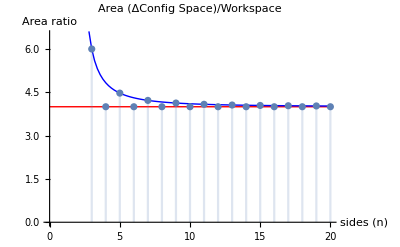

```mathematica
maxsides = 20;
DiscretePlot[If[EvenQ[sides],4,4 Sec[π/sides] Sin[(π Floor[sides/2])/sides]^2],{sides,3,maxsides},PlotRange->{{0,maxsides},{0,6.5}}, AxesLabel->{"sides (n)","Area ratio"},PlotLabel->"Area (ΔConfig Space)/Workspace",Prolog->{Red,Line[{{0,4},{20,4}}],Blue,Line[Table[{n,4 Sec[π/n] Sin[(π (n-1)/2)/n]^2},{n,2.8,20,.2}]]}]
```

```mathematica
Row[BoundaryMeshRegion[{{2,5},{6,3},{1,1},{3,4}}]]
```

Row[BoundaryMeshRegion[{{2,5},{6,3},{1,1},{3,4}}]]

```mathematica
??ConvexHullMesh
```

ConvexHullMesh[{p_1,p_2,…}] gives a BoundaryMeshRegion representing the convex hull from the points p_1, p_2, ….

Attributes[ConvexHullMesh]={Protected}
 
Options[ConvexHullMesh]={AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→False,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→False,BoxRatios→Automatic,BoxStyle→{},ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FaceGrids→None,FaceGridsStyle→{},Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},Lighting→Automatic,MeshCellHighlight→{},MeshCellLabel→Automatic,MeshCellMarker→0,MeshCellShapeFunction→Automatic,MeshCellStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme→Automatic,Prolog→{},Properties→{},RotateLabel→True,RotationAction→Fit,SphericalRegion→False,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→Automatic,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1}}

```mathematica
??Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

Attributes[Show]={Protected,ReadProtected}

```mathematica
{-1,-1}+3.5
```

{2.5,2.5}

```mathematica
BaselinePosition
```

```mathematica
AlignmentPoint
```

```mathematica
sides = 5;
v=Table[{Cos[2 (π n)/sides],Sin[2 (π n)/sides]},{n,1,sides}];
MeshCoordinates[ConvexHullMesh[Flatten[Table[(#-v⟦n⟧)&/@v,{n,1,sides}],1]]]
```